```mathematica
Quit[]
```

## Init

```mathematica
(* The following functions are needed for the analysis and are defined in the paper. *)
fA12[x_]:=If[x≥1,ArcSin[√(1/x)]^2,-1/4(Log[(1+√(1-x))/(1-√(1-x))]-ⅈ π)^2]
F12[x_]:=-2x(1+(1-x)fA12[x])
F12L=Limit[F12[x],x->Infinity];
CR[x_,mT_,ct_,cg_]:=ct+cg F12L/Re[F12[(4 mT^2)/x^2]]
CI[ct_,cg_]:=ct;
cr[x_,mt_,MT_]:=Re[F12[(4 MT^2)/x^2]]/Re[F12[(4 mt^2)/x^2]]
ci[x_,mt_,MT_]:=Piecewise[{{Im[F12[(4 MT^2)/x^2]]/Im[F12[(4 mt^2)/x^2]],x>2mt},{0,x≤2mt}}]
cir[x_,mt_,MT_]:=ci[x,mt,MT]/cr[x,mt,MT]
mt=173.2;

(* This section is just the Bayesian Fitting Algorithm to get the contours. *)

RR[x_,y_]:=RandomReal[{x,y}];RV[x_,σ_]:=RandomReal[NormalDistribution[x,σ]];
C68=N[PDF[NormalDistribution[0,1],1]/PDF[NormalDistribution[0,1],0]];
C95=N[PDF[NormalDistribution[0,1],2]/PDF[NormalDistribution[0,1],0]];
C99=N[PDF[NormalDistribution[0,1],3]/PDF[NormalDistribution[0,1],0]];
Fitctcg[x_,y_]:=Reap[
nit=x;ctm=0.1;cgm=0.1;dist={{RR[-1,2],RR[-2,2]}};PR={};
Do[ctt=dist[[-1,1]];cgt=dist[[-1,2]];ctn=RV[ctt,Abs[1*ctm]];cgn=RV[cgt,Abs[1*cgm]];prd[i]=Product[PND[j]/.{ct->ctt,cg->cgt},{j,Length[BinDef]-1}];prt[i]=Product[PND[j]/.{ct->ctn,cg->cgn},{j,Length[BinDef]-1}];r[i]=prt[i]/prd[i];If[r[i]≥RR[0,1],dist=Append[dist,{ctn,cgn}];PR=Join[PR,{prt[i]}],aa],{i,nit}];ctmean=Sum[dist[[i+1,1]]PR[[i]],{i,Length[PR]}]/Sum[PR[[i]],{i,Length[PR]}];cgmean=Sum[dist[[i+1,2]]PR[[i]],{i,Length[PR]}]/Sum[PR[[i]],{i,Length[PR]}];ctvar=Sum[dist[[i+1,1]]^2 PR[[i]],{i,Length[PR]}]/Sum[PR[[i]],{i,Length[PR]}]-ctmean^2;cgvar=Sum[dist[[i+1,2]]^2 PR[[i]],{i,Length[PR]}]/Sum[PR[[i]],{i,Length[PR]}]-cgmean^2;Ran:={ct->RR[ctmean-5 √ctvar,ctmean+5 √ctvar],cg->RR[cgmean-5 √cgvar,cgmean+5 √cgvar]};npar=y;Clear[Dist];Dist=ParallelTable[Reap[Ranp=Ran;PPr=Product[PND[i]/.Ranp,{i,Length[BinDef]-1}];Sow[{If[PPr≥C99*NORM&&PPr<C95*NORM,Flatten[{Pr->PPr,Ranp}],0],If[PPr≥C95*NORM&&PPr<C68*NORM,Flatten[{Pr->PPr,Ranp}],0],If[PPr≥C68*NORM,Flatten[{Pr->PPr,Ranp}],0]}]][[2,1,1]],{k,npar}];Dist1=DeleteCases[Dist[[All,1]],0];Dist2=DeleteCases[Dist[[All,2]],0];Dist3=DeleteCases[Dist[[All,3]],0];DistA=Join[Dist1,Dist2,Dist3];ctMean=Sum[ct*Pr/.DistA[[i]],{i,Length[DistA]}]/Sum[Pr/.DistA[[i]],{i,Length[DistA]}];cgMean=Sum[cg*Pr/.DistA[[i]],{i,Length[DistA]}]/Sum[Pr/.DistA[[i]],{i,Length[DistA]}];ctVar=Sum[ct^2*Pr/.DistA[[i]],{i,Length[DistA]}]/Sum[Pr/.DistA[[i]],{i,Length[DistA]}]-ctMean^2;cgVar=Sum[cg^2*Pr/.DistA[[i]],{i,Length[DistA]}]/Sum[Pr/.DistA[[i]],{i,Length[DistA]}]-cgMean^2;TableForm[{TableForm[{{ctMean,√ctVar},{cgMean,√cgVar}}]}]][[1]]

(* This function is for reading the files and setting up the analysis. Notice that the bins are interpolated at order 0 and then integrated into the larger bins. This is slightly different from what was done in the paper but is numerically insignificant. *)

MS[dir_,part_,en_,out_,set_]:=TableForm[Reap[SetDirectory[dir<>part];set[128]=Take[Import["HZZ_tb_lord_mstw8lo_0___0___126_128_run_"<>en<>".dat"],{265,459}];set[129]=Take[Import["HZZint_lord_mstw8lo_0___0___126_129_run_"<>en<>".dat"],{265,459}];set[130]=Take[Import["HZZH+i_lord_mstw8lo_0___0___126_130_run_"<>en<>".dat"],{265,459}];set[131]=Take[Import["ggZZ4l_lord_mstw8lo_0___0___126_131_run_"<>en<>".dat"],{265,459}];set[132]=Take[Import["ggZZbx_lord_mstw8lo_0___0___132_run_"<>en<>".dat"],{265,459}];Do[ANAI[j]=Interpolation[Drop[set[j][[All,1;;2]],{1,14}],InterpolationOrder->0],{j,128,132}];PL=GraphicsRow[Table[Quiet[LogLogPlot[Abs[ANAI[i][x]],{x,250,1500},Frame->True,Axes->False,PlotLabel->ToString[i]]],{i,128,132}],ImageSize->{1150,160},Spacings->-20];out=Table[Table[LUM*NIntegrate[ANAI[j][x],{x,BinDef[[i]],BinDef[[i+1]]}],{i,Length[BinDef]-1}],{j,128,132}];Sow[PL];Sow[(Table[Sum[out[[i,j]],{i,{1,2,5}}],{j,Length[BinDef]-1}]-out[[4]])/out[[4]]*100]][[2]]]

origBin=Range[245,1505,10];
BinDef={250,400,600,800,1100,1500};
MT=1000; (*Analysis done with a 1 TeV heavy top*)
```

## Analysis 14 TeV

```mathematica
MSTW=NotebookDirectory[]<>"Data/E_var_1T/E_14/MSTW/";
LUM=0.95^4*2*1.85*3000;
LUMT=LUM;
LUMB=0.95^4*2*3000;
```

### Read files for SM TOP

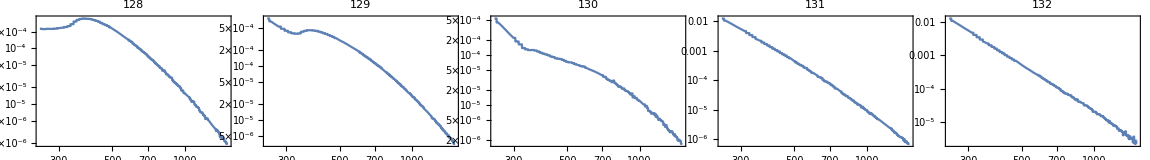
-Graphics- | 0.0197769
0.23758
-2.90946
0.400091
-1.81407

```mathematica
Clear[BINDT14];MS[MSTW,"TOP","14",BINDT14,SETT14]
```

### Read files for 1 TeV TOP PARTNER

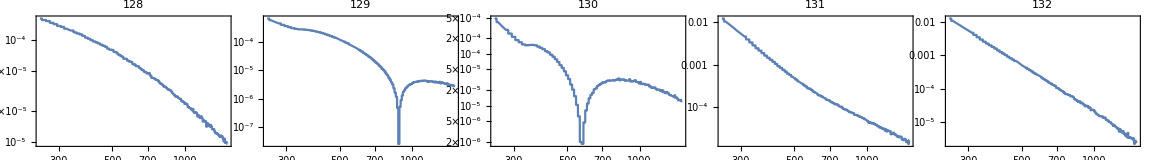
-Graphics- | 0.0536957
-0.259494
-0.980078
0.0499749
0.0895635

```mathematica
Clear[BINDHHT14];MS[MSTW,"HHTOP","14",BINDHHT14,SETHHT14]
```

### Signal and Background

```mathematica
S128HHT14=Table[Append[Drop[SETHHT14[128][[i]],-1],(SETHHT14[128][[i,2]])/cr[SETHHT14[128][[i,1]],mt,MT]^2],{i,Length[SETHHT14[128]]}];
S129HHT14=Table[Append[Drop[SETHHT14[129][[i]],-1],(SETHHT14[129][[i,2]])/cr[SETHHT14[129][[i,1]],mt,MT]],{i,Length[SETHHT14[129]]}];

F0=Table[{SETT14[132][[i,1]],LUMT*SETT14[132][[i,2]]},{i,15,Length[SETT14[132]]}];(* F0 *)
F1=Table[{S128HHT14[[i,1]],LUMT*S128HHT14[[i,3]]},{i,15,Length[S128HHT14]}];(* F1 *)
F2=Table[{SETT14[128][[i,1]],LUMT*SETT14[128][[i,2]]-F1[[i-14,2]]},{i,15,Length[SETT14[128]]}];(* F2 *)
F3=Table[{S129HHT14[[i,1]],LUMT*S129HHT14[[i,3]]},{i,15,Length[S129HHT14]}];(* F3 *)
F4=Table[{SETT14[129][[i,1]],LUMT*SETT14[129][[i,2]]-F3[[i-14,2]]},{i,15,Length[SETT14[129]]}];(* F4 *)
EQM=Table[{F0[[i,1]],Expand[F0[[i,2]]+F1[[i,2]] CR[F1[[i,1]],mt,ct,cg]^2+F2[[i,2]] ct^2+F3[[i,2]]CR[F1[[i,1]],mt,ct,cg]+F4[[i,2]]ct]},{i,Length[F0]}];
CL=Normal[CoefficientArrays[EQM[[All,2]],{ct,cg}]];

COA=Table[NIntegrate[Interpolation[Table[{EQM[[i,1]],CL[[1]][[i]]},{i,Length[EQM]}],InterpolationOrder->1][x],{x,BinDef[[j]],BinDef[[j+1]]}],{j,Length[BinDef]-1}];(*const*)
CTA=Table[NIntegrate[Interpolation[Table[{EQM[[i,1]],CL[[2,All,1]][[i]]},{i,Length[EQM]}],InterpolationOrder->1][x],{x,BinDef[[j]],BinDef[[j+1]]}],{j,Length[BinDef]-1}];(*ct*)
CGA=Table[NIntegrate[Interpolation[Table[{EQM[[i,1]],CL[[2,All,2]][[i]]},{i,Length[EQM]}],InterpolationOrder->1][x],{x,BinDef[[j]],BinDef[[j+1]]}],{j,Length[BinDef]-1}];(*cg*)
CT2A=Table[NIntegrate[Interpolation[Table[{EQM[[i,1]],CL[[3,All,1]][[All,1]][[i]]},{i,Length[EQM]}],InterpolationOrder->1][x],{x,BinDef[[j]],BinDef[[j+1]]}],{j,Length[BinDef]-1}];(*ct^2*)
CTCGA=Table[NIntegrate[Interpolation[Table[{EQM[[i,1]],CL[[3,All,1]][[All,2]][[i]]},{i,Length[EQM]}],InterpolationOrder->1][x],{x,BinDef[[j]],BinDef[[j+1]]}],{j,Length[BinDef]-1}](*ct cg*)
CG2A=Table[NIntegrate[Interpolation[Table[{EQM[[i,1]],CL[[3,All,2]][[All,2]][[i]]},{i,Length[EQM]}],InterpolationOrder->1][x],{x,BinDef[[j]],BinDef[[j+1]]}],{j,Length[BinDef]-1}];(*cg^2*)

EQN[ct_,cg_]:=COA+CTA ct+CGA cg+CT2A ct^2+CTCGA ct cg+CG2A cg^2;

SetDirectory[NotebookDirectory[]<>"Data/background_NLO_nogg/E_14"];
BG[4]=Import["ZZlept_tota_mstw8nl_0___0___81_14_M.dat"];
BGE[4]=Take[BG[4],{265,459}];
BGI[4]=Table[LUMB*NIntegrate[Interpolation[Drop[BGE[4][[All,1;;2]],{1,8}],InterpolationOrder->0][x],{x,BinDef[[j]],BinDef[[j+1]]}],{j,Length[BinDef]-1}];
ANB=Table[{(EQN[ct,cg][[i]]/.{ct->1,cg->0}),√(BGI[4][[i]])},{i,Length[BinDef]-1}];
```

{498.003,391.753,99.693,23.8956,-2.38868}

```mathematica
EQN[ct,cg]//TableForm
```

7084.55-479.773 cg+178.364 cg^2-665.761 ct+498.003 cg ct+361.988 ct^2
1162.15-231.695 cg+142.582 cg^2-564.907 ct+391.753 cg ct+424.664 ct^2
226.491-42.7186 cg+82.6646 cg^2-217.155 ct+99.693 cg ct+144.28 ct^2
84.4202+3.2912 cg+66.9799 cg^2-104.166 ct+23.8956 cg ct+61.3955 ct^2
22.726+11.6161 cg+40.8005 cg^2-32.1863 ct-2.38868 cg ct+17.2075 ct^2

## Fitting m_(4l)/2 14 TeV

### Non-linearized

0.85141 | 0.282364
-0.148055 | 0.296732

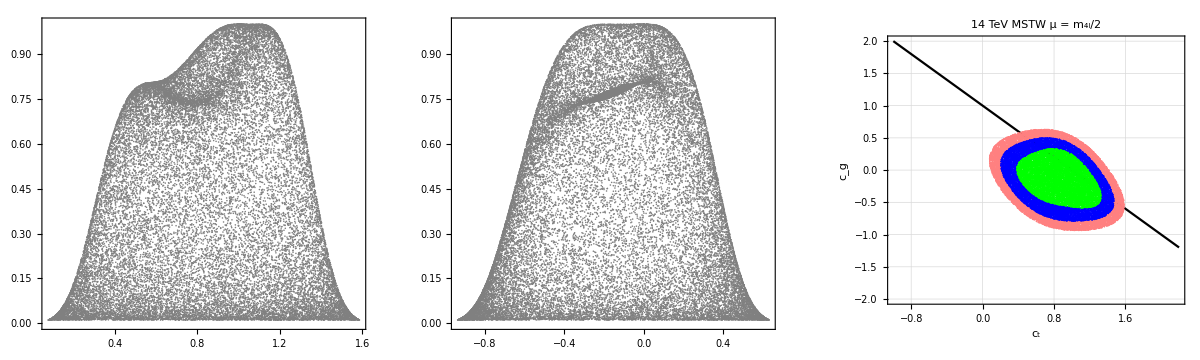

```mathematica
Do[Thlist[i]=EQN[ct,cg][[i]],{i,Length[EQN[ct,cg]]}];
PND[i_]:=PDF[NormalDistribution[ANB[[i]][[1]],ANB[[i]][[2]]],Thlist[i]];
NORM=Product[PND[j]/.{ct->1,cg->0},{j,Length[BinDef]-1}];
Fitctcg[10000,100000]
GraphicsRow[Table[ListPlot[Table[{DistA[[i,j,2]],DistA[[i,1,2]]/NORM},{i,Length[DistA]}],PlotRange->All,Frame->True,Axes->False,PlotStyle->Gray],{j,2,3}]~Join~{ListPlot[{Table[{Range[-1.0,2.2,0.1][[i]],1-Range[-1.0,2.2,0.1][[i]]},{i,Length[Range[-1.0,2.2,0.1]]}],Table[{Dist1[[i,2,2]],Dist1[[i,3,2]]},{i,Length[Dist1]}],Table[{Dist2[[i,2,2]],Dist2[[i,3,2]]},{i,Length[Dist2]}],Table[{Dist3[[i,2,2]],Dist3[[i,3,2]]},{i,Length[Dist3]}]},PlotRange->{{-1,2.2},{-2,2}},Frame->True,Axes->False,PlotStyle->{Black,Pink,Blue,Green},AspectRatio->1,Joined->{True,False,False,False},FrameLabel->{"c_t","c_g"},PlotLabel->"14 TeV MSTW μ = m_(4l)/2",GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed]]},ImageSize->{1200,360}]
```

### linearized

-0.000337077 | 0.651175
0.000788437 | 0.920971

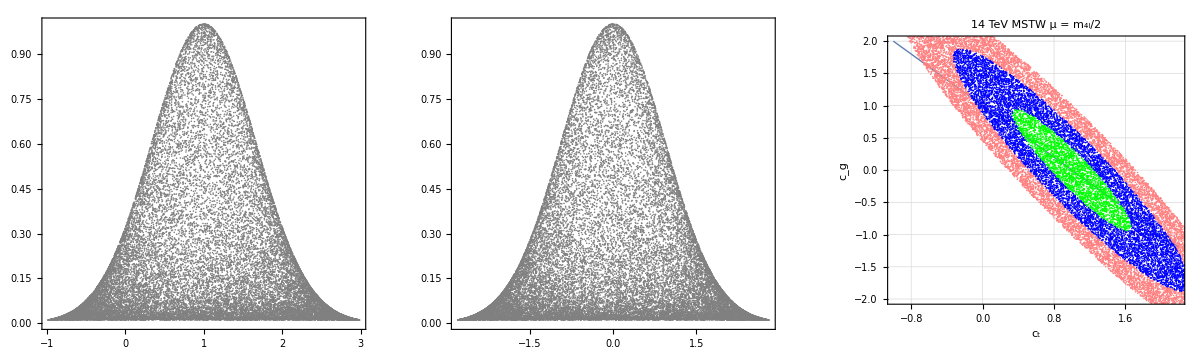

```mathematica
Do[Thlist[i]=Expand[Normal[Series[EQN[ct,cg][[i]]/.{ct->1+ct},{ct,0,1}]]]/.{cg^2->0,cg ct->0},{i,Length[EQN[ct,cg]]}]
PND[i_]:=PDF[NormalDistribution[ANB[[i]][[1]],ANB[[i]][[2]]],Thlist[i]];
NORM=Product[PND[j]/.{ct->0,cg->0},{j,Length[BinDef]-1}];
Fitctcg[10000,100000]
GraphicsRow[Table[ListPlot[Table[{Abs[j-3]+DistA[[i,j,2]],DistA[[i,1,2]]/NORM},{i,Length[DistA]}],PlotRange->All,Frame->True,Axes->False,PlotStyle->Gray],{j,2,3}]~Join~{ListPlot[{Table[{Range[-1.0,2.2,0.1][[i]],1-Range[-1.0,2.2,0.1][[i]]},{i,Length[Range[-1.0,2.2,0.1]]}],Table[{1+Dist1[[i,2,2]],Dist1[[i,3,2]]},{i,Length[Dist1]}],Table[{1+Dist2[[i,2,2]],Dist2[[i,3,2]]},{i,Length[Dist2]}],Table[{1+Dist3[[i,2,2]],Dist3[[i,3,2]]},{i,Length[Dist3]}]},PlotRange->{{-1,2.2},{-2,2}},Frame->True,Axes->False,PlotStyle->{Thick,Pink,Blue,Green},AspectRatio->1,Joined->{True,False,False,False},FrameLabel->{"c_t","c_g"},PlotLabel->"14 TeV MSTW μ = m_(4l)/2",GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed]]},ImageSize->{1200,360}]
```